# The Walking Dead

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
<<PajaroLocoPublic`
nonMigratoryForce=1000;
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
CalculateMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ListPlotPoints[points_]:=ListPlot[points,
Frame->True,
Axes->True,
FrameStyle->Thickness[.005],
ImageSize->800,
FrameTicksStyle->None,
PlotStyle->PointSize[.025],
AspectRatio->1
]Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
Themes`AddThemeRules["RandomPointsPlot",
AspectRatio->1,
Frame->True,
FrameLabel->(Style[#,20]&/@{"x (meters)","y (meters)"}),
FrameTicksStyle->20,
FrameStyle->Thick,
FrameTicks->{{None,All},{None,All}},
PlotStyle->Directive[PointSize[.02],Opacity[.75]],
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
Themes`AddThemeRules["RandomPointsMatrix",
AspectRatio->1,
Frame->True,
FrameStyle->Thick,
FrameTicks->{{None,None},{None,None}},
ColorFunction->"LakeColors",
AxesStyle->Directive[{Opacity[.25],Thick,Gray}]
]
DistributionIntoKernel[distribution_,center_,n_]:=Table[center+{Re[#],Im[#]}&[RandomReal[distribution] ⅇ^(ⅈ RandomReal[{0,2π}])],{n}]
MapDistributionParametersOnPoints[distribution_,centers_,n_]:=Join@@(DistributionIntoKernel[distribution,#,n]&/@centers)
SphereDistance[{ϕ1_,θ1_},{ϕ2_,θ2_},r_]:=r InverseHaversine[Haversine[ϕ1-ϕ2]+Cos[ϕ1]Cos[ϕ2]Haversine[θ1-θ2]]
SphereDistanceBetweenPoints[sphericalCoordinates1_,sphericalCoordinates2_]:=Module[{tuple},
tuple={
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates1],
CoordinateTransformData["Cartesian"->"Spherical", "Mapping",sphericalCoordinates2]
};
SphereDistance[{tuple[[1,2]],tuple[[1,3]]},{tuple[[2,2]],tuple[[2,3]]},tuple[[1,1]]]
]
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameTicks->{None,None},
Filling->Bottom,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
BaseStyle->15,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Opacity[.5]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
GenerateAccumulatedCoordinates[coordinatesRange_,citiesNumber_]:=Module[{sampledCoordinates,citiesDummy,names,pops,cities},
(*Generate Random Coordinates*)
sampledCoordinates=citiesDummy = Accumulate[RandomReal[{-coordinatesRange,coordinatesRange}, {citiesNumber, 2}]];
names = ToString /@ Range[citiesDummy // Length];
pops = RandomInteger[1000, citiesDummy // Length];
cities = Transpose[{names, citiesDummy, pops}];
{sampledCoordinates,names,pops,cities}
]
SyllableToID[a_,labels_]:=Position[labels,a]
ConvertSyllablesToID[sample_,syllablesLabels_]:=Table[SyllableToID[sample[[i]],syllablesLabels],{i,1,Length[sample]}]//Flatten
InTuples[communitiesList_,syllablesLabels_]:=Module[{communitiesIndexes},communitiesIndexes=Map[(Map[Position[syllablesLabels,#]&,#]//Flatten)&,communitiesList];
Tuples[#,2]&/@communitiesIndexes]
ListPlotSong[sample_,syllablesLabels_,OptionsPattern[]]:=Module[{texts,g},texts=Graphics[Text[Style[ToString[#[[1]]],OptionValue[TextSize]],{(sample//Length)+10,#[[2]]},Automatic],AspectRatio->1]&/@({syllablesLabels,Range[syllablesLabels//Length]}//Transpose);
g=ListPlot[
If[OptionValue[Labeling]==True,Labeled[#[[1]],#[[2]]]&,Tooltip[#[[1]],#[[2]]]&]/@({ConvertSyllablesToID[sample,syllablesLabels],ToString/@sample}//Transpose),
ImageSize->OptionValue[ImageSize],
PlotStyle->Directive[Opacity[.75],PointSize[Medium]],
Filling->None,
AxesLabel->{"TimeStep","ID"},
PlotRange->{0,syllablesLabels//Length},
ImagePadding->50,
GridLines->Automatic,
GridLinesStyle->Directive[LightBlue],
Frame->True,
FrameStyle->Directive[Thick,Black],
FrameTicksStyle->20
];
Show[g,texts,PlotRange->{0,(syllablesLabels//Length)+1}]
]
CalculateInOutRatio[inOutList_]:=(inOutList[[1]]/(inOutList[[1]]+inOutList[[2]]))
ListPlotSongWithCommunities[sample_,communities_,colors_,OptionsPattern[]]:=Module[{frequencyOutput,inOutTotals,labels2,individualCommunitiesInOutRatios,texts,connectionsRules,connectionsWithLabels,rect,rectangles,listPlot,sortedCommunities,wrappers,communitiesIDs,wrappersID},
frequencyOutput=GetTransitionsFrequencies[sample];
inOutTotals=GetCommunitiesInOutTransitionsFrequencies[frequencyOutput,communities,CountLoops->OptionValue[CountLoops]];
labels2=communities//Flatten//DeleteDuplicates;
sortedCommunities=Table[SortBy[i,Position[labels2,#]&],{i,communities}];
wrappers={(#//First)&/@sortedCommunities,(#//Last)&/@sortedCommunities}//Transpose;
communitiesIDs=Table[Position[labels2,#]&/@i//Flatten,{i,sortedCommunities}];
wrappersID={(#//First)&/@communitiesIDs,(#//Last)&/@communitiesIDs}//Transpose;
connectionsRules=wrappersID;
connectionsWithLabels=(UndirectedEdge[labels2[[#[[1]]]],labels2[[#[[2]]]]])&/@connectionsRules;
rect=Rectangle[{0.5,#[[1]]},{(sample//Length)+.5,#[[2]]},RoundingRadius->0]&/@connectionsRules;
rectangles=Graphics[
{
EdgeForm[Directive[Dashing[RandomReal[{0,0}]],Thickness[RandomReal[{.00175,.00175}]],Opacity[.2],colors[[#[[3]]]]]],Opacity[.2],colors[[#[[3]]]],#[[1]]
}
,ImagePadding->500]&/@({rect,Table[i[[1]]/(labels2//Length),{i,wrappersID}],Range[wrappersID//Length]}//Transpose);
individualCommunitiesInOutRatios=CalculateInOutRatio[#]&/@(inOutTotals//Transpose);
texts=Graphics[Text[Style[ToString[PaddedForm[#[[1]],{4,4}]],Bold,OptionValue[TextSize]],{(sample//Length)/2,#[[2]]+.35},Automatic],AspectRatio->1]&/@({individualCommunitiesInOutRatios,connectionsRules[[All,1]]}//Transpose);
listPlot=ListPlotSong[sample,labels2,ImageSize->OptionValue[ImageSize],Labeling->OptionValue[Labeling],TextSize->OptionValue[TextSize]];
Show[{listPlot,rectangles,texts}//Flatten]
]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

RandomPointsPlot

RandomPointsMatrix

## Inputs

```mathematica
{vertexSize,vertexLabelSize}={2,10};
(*Set the number of cities wanted, the x-y coordinates range to sample from, and the number of site types allowd*)
{citiesNumber,coordinatesRange,classesNumber}={50,100,4};
(*Assigns a class type to each point based on a random uniform distribution of probabilities and the number of types defined previously*)
(*Set a vector with the probabilities the walker has to stay in current node or move to the others. This vector is then rotated to generate the "partiteness" mask.*)
directionStrength=1;
movementProbabilitiesVector={1-directionStrength,directionStrength*.9,directionStrength*.1,0};
(*The penalizations matrix is a type-based transitions matrix to be used as mask down the road*)
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,classesNumber}];
MatrixForm[penalizationsMatrix]
```

(0 | 0.9 | 0.1 | 0
0 | 0 | 0.9 | 0.1
0.1 | 0 | 0 | 0.9
0.9 | 0.1 | 0 | 0)

## Generate Random Spatial Setting

{{1,2,3,4,5,8,9,10,11,12,13,14,15,16},{6,7},{17,18,19,20,21,22,28},{23,24,25,26,27,29,30,34,35,36},{31,32,33,37,38},{39,44,45},{40,41,43,46},{42},{47},{48,50},{49}}

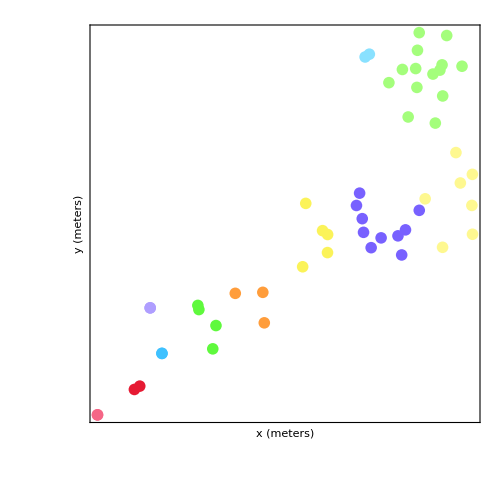

```mathematica
(*This is a very basic algorithm to generate points in a landscape. Replace it with a better later on.*)
{sampledCoordinates,names,pops,cities}=GenerateAccumulatedCoordinates[-100,citiesNumber];
distances = CalculateEuclideanDistances[sampledCoordinates];
(*Geo-Clustering*)
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
clustersStrings=Table[ToString/@Flatten[Position[cities[[All,2]],#]&/@clusteredCoordinates[[i]]],{i,1,clusteredCoordinates//Length}]
clustersIDs=Position[Map[ToExpression,clustersStrings,Infinity],#][[1,1]]&/@Range[Length[sampledCoordinates]];
(*Plots*)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clustersStrings])]]//Flatten//RandomSample;
ListPlot[clusteredCoordinates,PlotTheme->"RandomPointsPlot",ImageSize->500,PlotStyle->colors]
```

## Analyze

Map

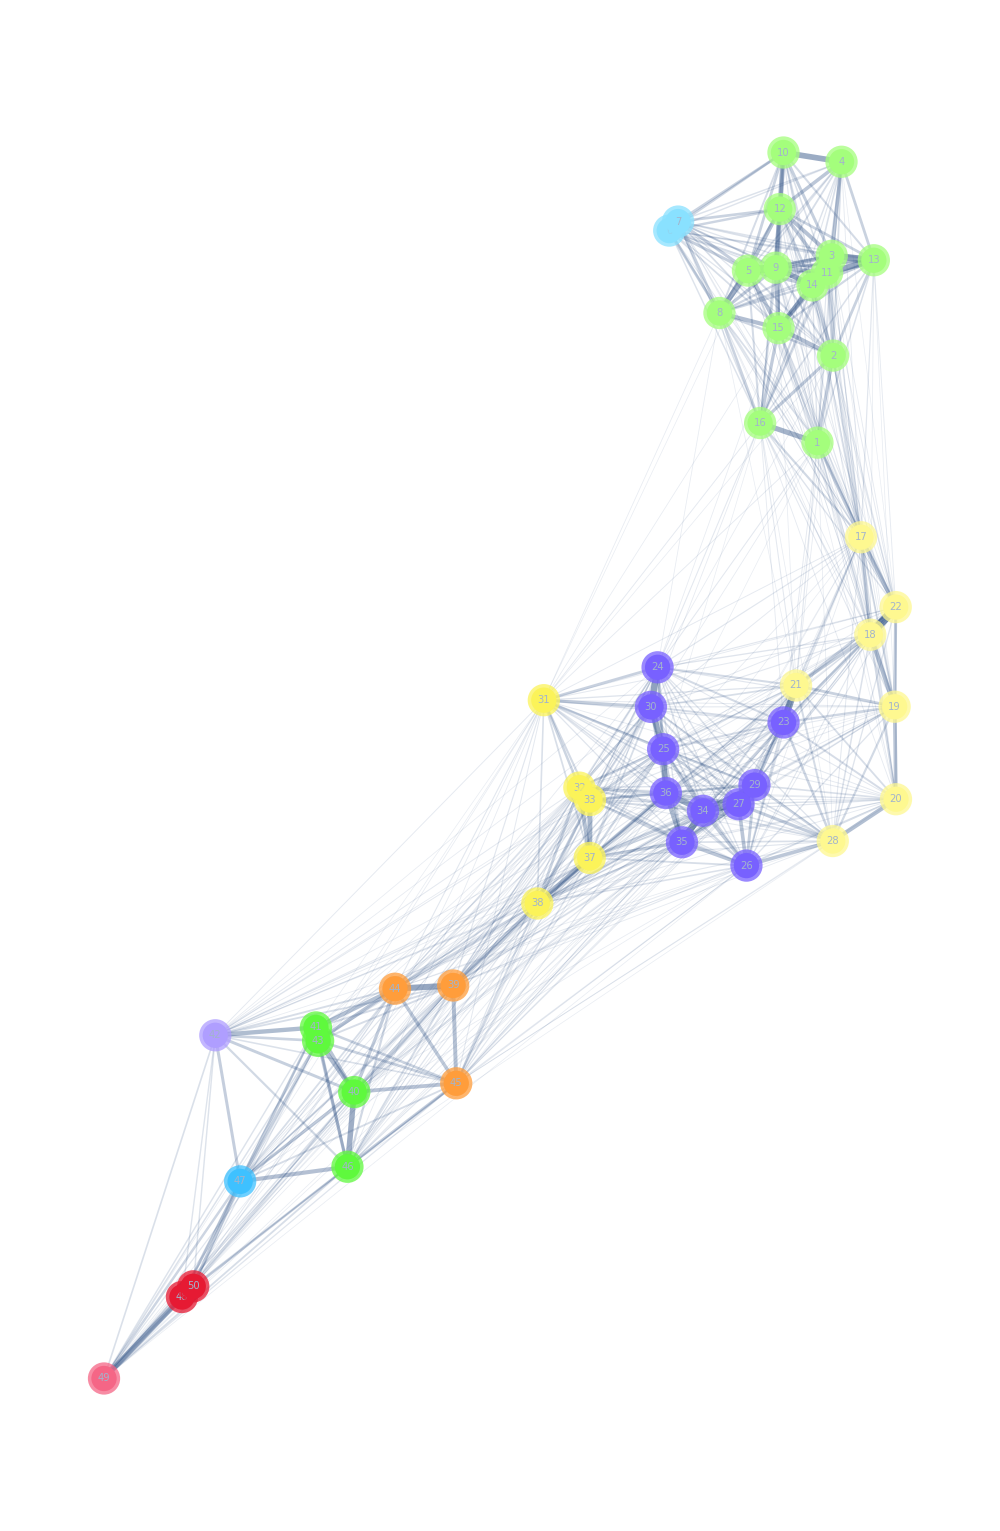

```mathematica
(*This "migration" is replacing the real kernel for the time being. It is based on the inverse of the distance to other nodes.*)
migration = CalculateMigrationProbabilities[distances, .05];
edgeshape2[e_,___]:={Arrowheads[{{.000001,.9}}],Arrow[e]}
stylesSwatch=Directive[Opacity[1],colors[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[clusteredCoordinates//Length];
stylesList=(ToString[#[[1]]]->stylesSwatch[[#[[2]]]])&/@Transpose[{Range[clustersIDs//Length],clustersIDs}];
map = GraphTransitionsFrequenciesWithMax[
  {
Chop[ReplacePart[migration,{i_,i_}->0]//LowerTriangularize,10^-2],
ToString /@ Range[Length[migration]]
   }, .15,
 VertexStyle ->stylesList,
VertexCoordinates ->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize -> 1000,
LineThickness -> .0075,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
```

```mathematica
Export["00_clustering.pdf",map,ImageSize->2000,ImageResolution->500]
```

00_clustering.pdf

Mask Movement with Site-Types

```mathematica
(*If the transition between city types is not possible, or improbable, then mask it with the corresponding value. After that, normalize for the probabilities to still add up to one.*)
cityType=RandomChoice[Range[classesNumber],citiesNumber]
{cityType[[1]],#}&/@cityType;
penalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
normalizedMaskedMatrix=(#/Total[#])&/@(penalizationsMask*migration);
(*Plots*)
penalizationsMaskPlot=penalizationsMask//MatrixPlot[#,ColorFunction -> "LakeColors", ImageSize ->500/2]&;
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/classesNumber]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
normalizedMaskedMatrixPlot=normalizedMaskedMatrix//MatrixPlot[#,ColorFunction->"LakeColors"]&;
```

{3,3,3,4,3,3,4,2,2,3,4,2,2,4,1,2,2,2,3,3,2,4,2,2,2,4,3,2,4,1,3,2,2,4,2,1,4,2,2,3,2,3,3,2,1,2,4,2,2,4}

Movement Network

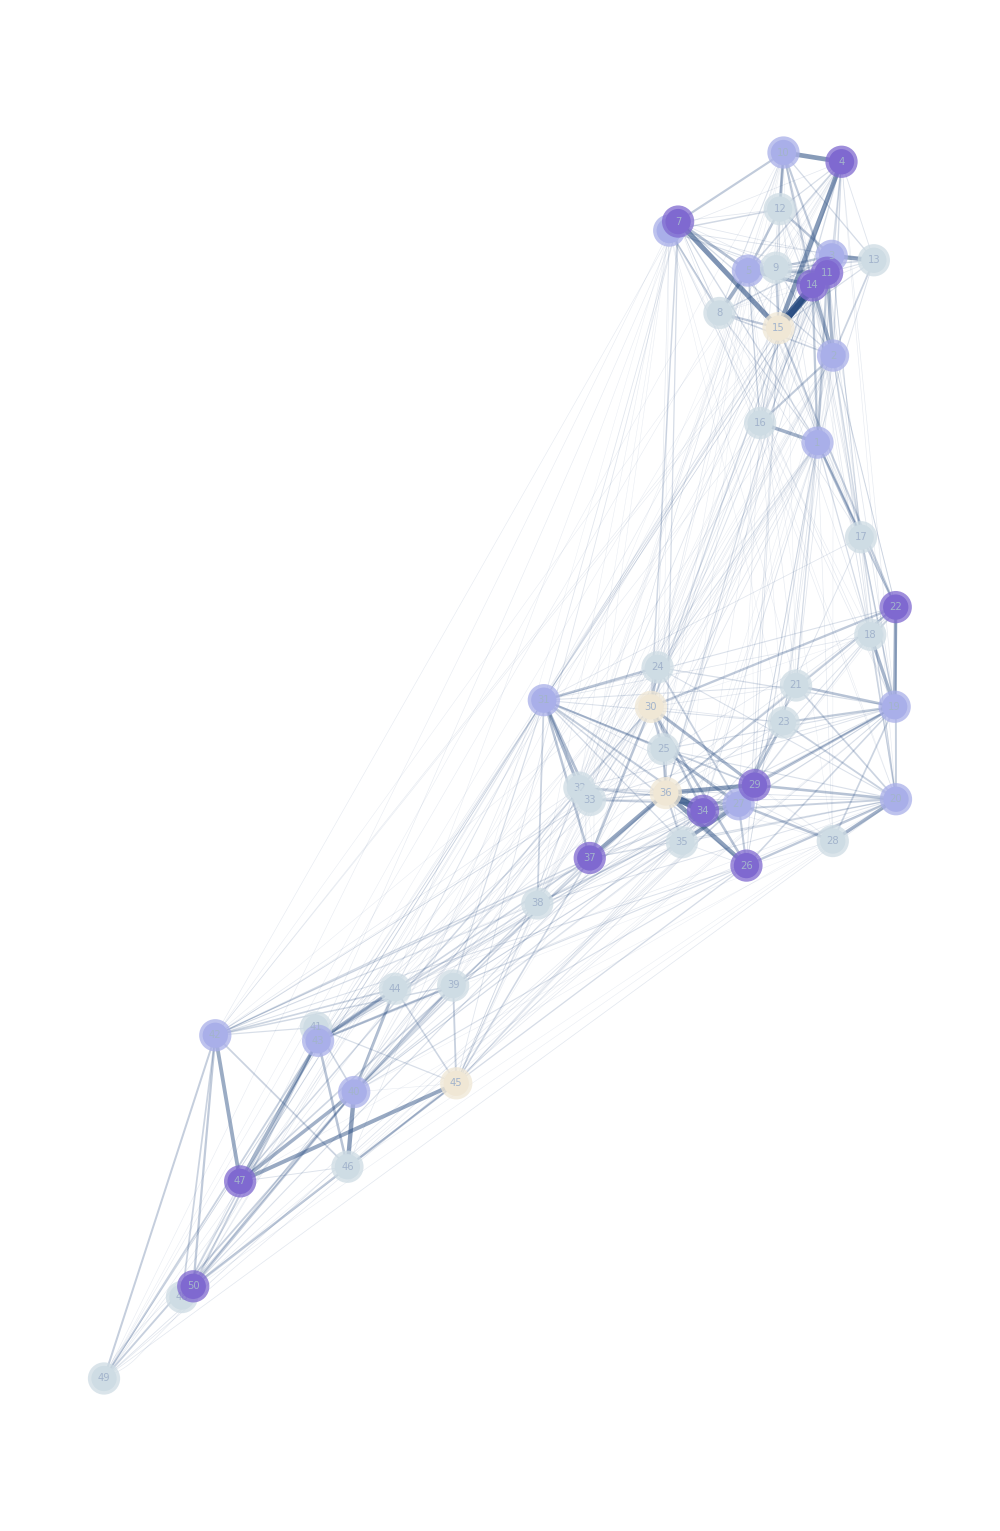

01_Movement.pdf

```mathematica
edgeshape2[e_,___]:={Arrowheads[{{.01,.75}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .5,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize ->vertexSize,
VertexLabelStyle->vertexLabelSize,
ImageSize->1000,
LineThickness->.005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["01_Movement.pdf",%,ImageSize->2000,ImageResolution->500]
```

Sink and Source

```mathematica
differenceThreshold=.3;
(**)
communities=Map[ToExpression,clustersStrings,Infinity]
outCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0];
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
inCommunity=Table[
comm=communities[[i]];
transitions=ReplacePart[normalizedMaskedMatrix,{i_,i_}->0]//Transpose;
Total[Total/@(Delete[transitions[[comm]]//Transpose,{#}&/@comm]//Transpose)]
,{i,1,Length[communities]}];
outMinusIn=outCommunity-inCommunity;
typeOfCommunity=If[Abs[#]<differenceThreshold,"Bridge",If[#>0,"Source","Sink"]]&/@outMinusIn
(**)
gridSourceSink=Grid[{
Style[PaddedForm[#,{3,3}],7.5,Bold]&/@outMinusIn,
Style[#,7.5,Bold]&/@typeOfCommunity
},
Frame->True,Background->{Lighter[#,0.1]&/@colors[[1;;Length[outMinusIn]]],None},ItemSize->3]
edges=Table[colors[[i]]&/@clustersStrings[[i]],{i,1,Length[clustersStrings]}]//Flatten;
flattenedRatios=Table[ConstantArray[typeOfCommunity[[i]],communities[[i]]//Length],{i,1,communities//Length}]//Flatten;
graphSinkSource=HighlightGraph[graph, Style[#[[2]] ,Directive[EdgeForm[Directive[Opacity[1],Switch[#[[3]],"Bridge",Black,"Sink",Darker[Blue,0],"Source",Darker[Red,0]],Thickness[.005]]],#[[1]]]] & /@ ({edges,clustersStrings//Flatten,flattenedRatios} // Transpose)];
```

{{1,2,3,4,5,8,9,10,11,12,13,14,15,16},{6,7},{17,18,19,20,21,22,28},{23,24,25,26,27,29,30,34,35,36},{31,32,33,37,38},{39,44,45},{40,41,43,46},{42},{47},{48,50},{49}}

{Bridge,Sink,Source,Sink,Sink,Source,Source,Bridge,Source,Bridge,Source}

0.032 | -0.323 |  0.472 | -1.130 | -1.440 |  0.526 |  0.667 |  0.089 |  0.318 |  0.048 |  0.746
Bridge | Sink | Source | Sink | Sink | Source | Source | Bridge | Source | Bridge | Source

Sinks and Sources Report

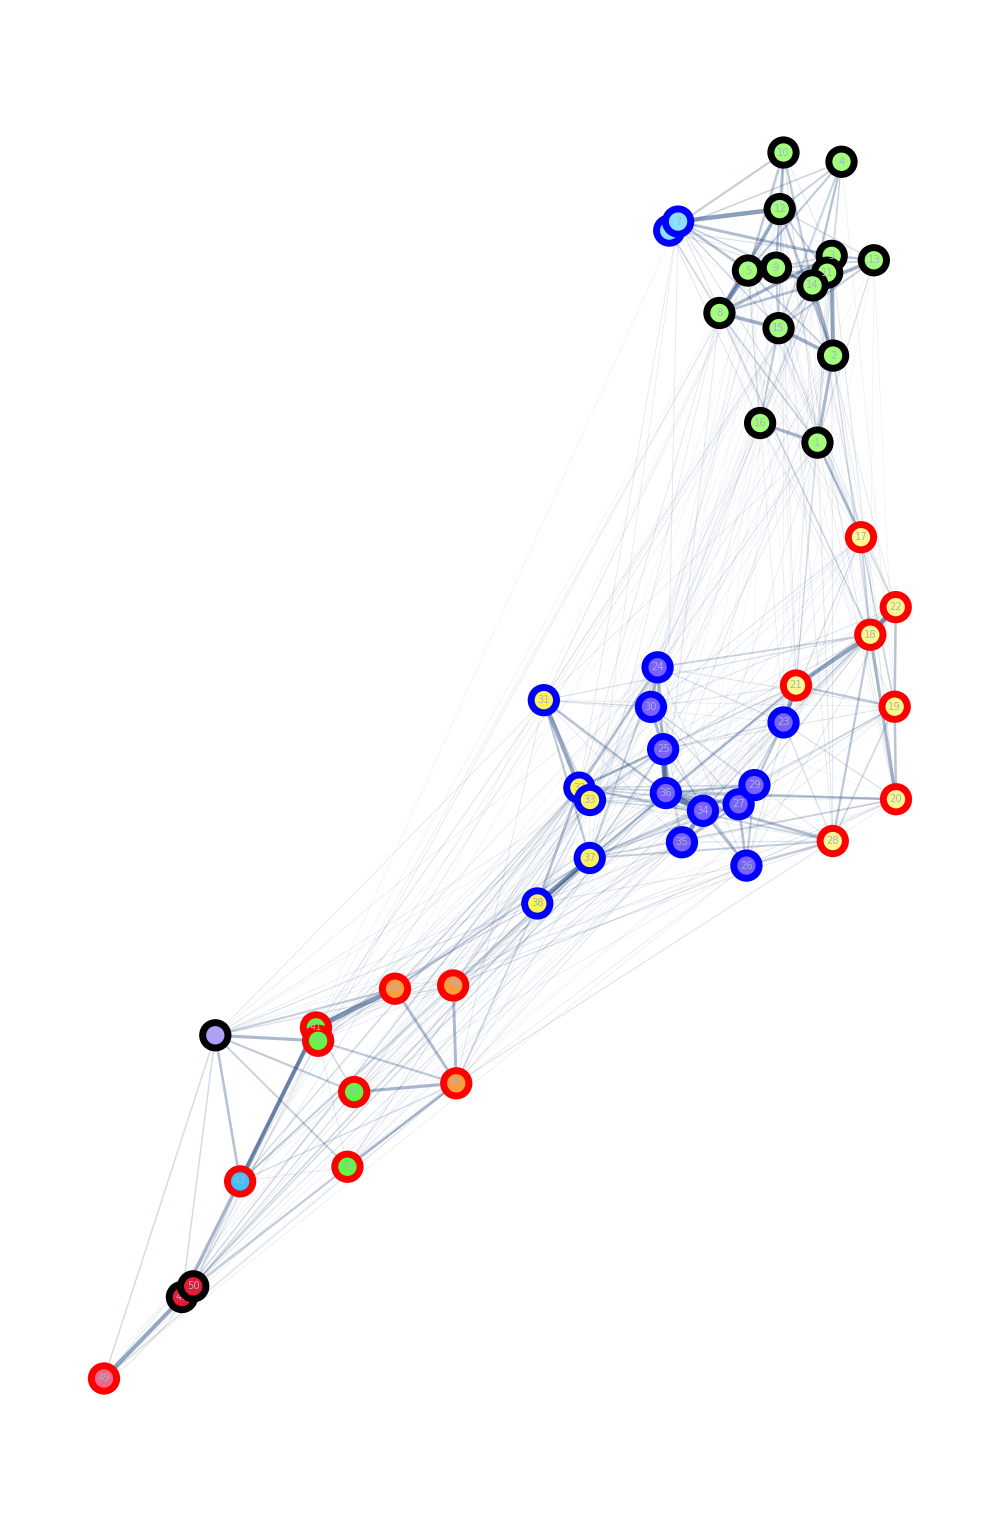
Clustered Map |  | Point Types |  | Sources (R) and Sinks(B)
-Graphics- | + | -Graphics- | = | -Graphics-
 0.032 | -0.323 |  0.472 | -1.130 | -1.440 |  0.526 |  0.667 |  0.089 |  0.318 |  0.048 |  0.746
Bridge | Sink | Source | Sink | Sink | Source | Source | Bridge | Source | Bridge | Source

02_grid.pdf

```mathematica
gridSinksAndSources=Grid[{
Style[#,25]&/@{"Clustered Map","","Point Types","","Sources (R) and Sinks(B)"},
{map,Style["+",Bold,50],graph,Style["=",Bold,50],Grid[{{graphSinkSource},{gridSourceSink}}]}
}]
Export["02_grid.pdf",%]
```

Centrality Analysis

```mathematica
BetweennessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
BetweennessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,0.,0.,0.,1.2544,0.,0.,6.32571,0.953159,0.,1.73855,0.201712,2.23379,2.23379,19.5374,40.8046,86.6527,54.6759,54.6759,11.2986,17.8454,91.6494,10.585,27.6106,21.2864,11.5042,9.6025,9.53166,8.12798,17.5546,73.9478,12.0007,12.0007,11.3279,11.3279,11.3279,20.6803,37.1296,18.0542,9.04338,2.3121,8.98891,0.947629,10.1872,11.6787,7.70872,5.14984,0.,1.30277,0.}

{108.396,104.122,118.976,34.4511,39.0462,22.4635,43.3655,56.0072,69.9575,17.7056,47.4489,81.3821,25.0495,99.8293,51.1051,118.447,35.5395,79.8146,98.6891,44.8614,51.0671,35.5395,39.8519,51.0671,51.0671,43.9669,60.9683,91.1563,70.6857,39.8519,51.0671,276.16,229.125,120.14,90.7651,158.617,166.427,35.865,135.187,70.7618,69.5273,63.932,105.105,127.345,63.932,84.4086,42.7159,100.154,20.8733,48.0127}

-Graphics-

```mathematica
ClosenessCentrality[map]
a=HighlightGraph[map,VertexList[map],VertexSize-> Thread[VertexList[map]-> Rescale[%]]];
ClosenessCentrality[graph]
b=HighlightGraph[graph,VertexList[graph],VertexSize-> Thread[VertexList[graph]-> Rescale[%]]];
Grid[{{a,b}}]
```

{0.,21.507,41.6291,31.6517,35.5513,42.5665,14.5615,25.7518,26.5923,28.9019,34.0315,21.9571,27.576,26.2215,25.4382,36.3459,54.6499,47.5854,48.2316,34.1674,32.6111,47.4558,32.5174,45.3455,45.7546,40.8578,39.3253,35.2982,33.5186,43.3735,49.6295,40.8001,33.3625,41.1455,38.0877,35.9222,38.9164,41.9718,39.4509,43.3305,35.6974,41.216,30.2693,37.9564,38.5013,40.2221,40.0919,30.4562,42.1442,33.3683}

{6.84537,8.13,6.40782,7.69528,6.21966,6.17195,7.44868,7.14082,5.46066,6.78801,5.84513,5.82913,6.79746,7.06482,6.87825,7.66257,7.13717,6.74472,7.40066,5.6692,6.07338,7.3198,5.81797,5.76165,6.78088,6.94101,6.26386,6.62149,6.14063,6.11246,5.97994,7.97257,7.32189,6.68776,7.26228,8.68534,8.30167,6.38673,8.50968,7.45999,6.09836,7.04008,7.50187,8.24215,7.14428,7.4121,7.99423,7.95906,8.91336,4.57609}

-Graphics-

Walkers

```mathematica
kernel=normalizedMaskedMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,3->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
```

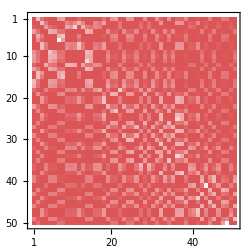
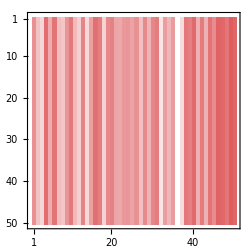
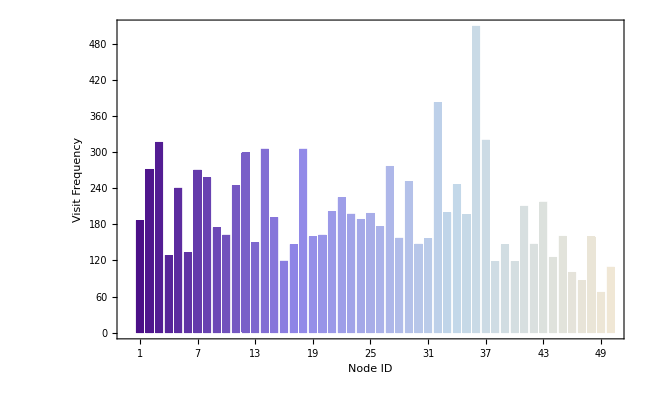
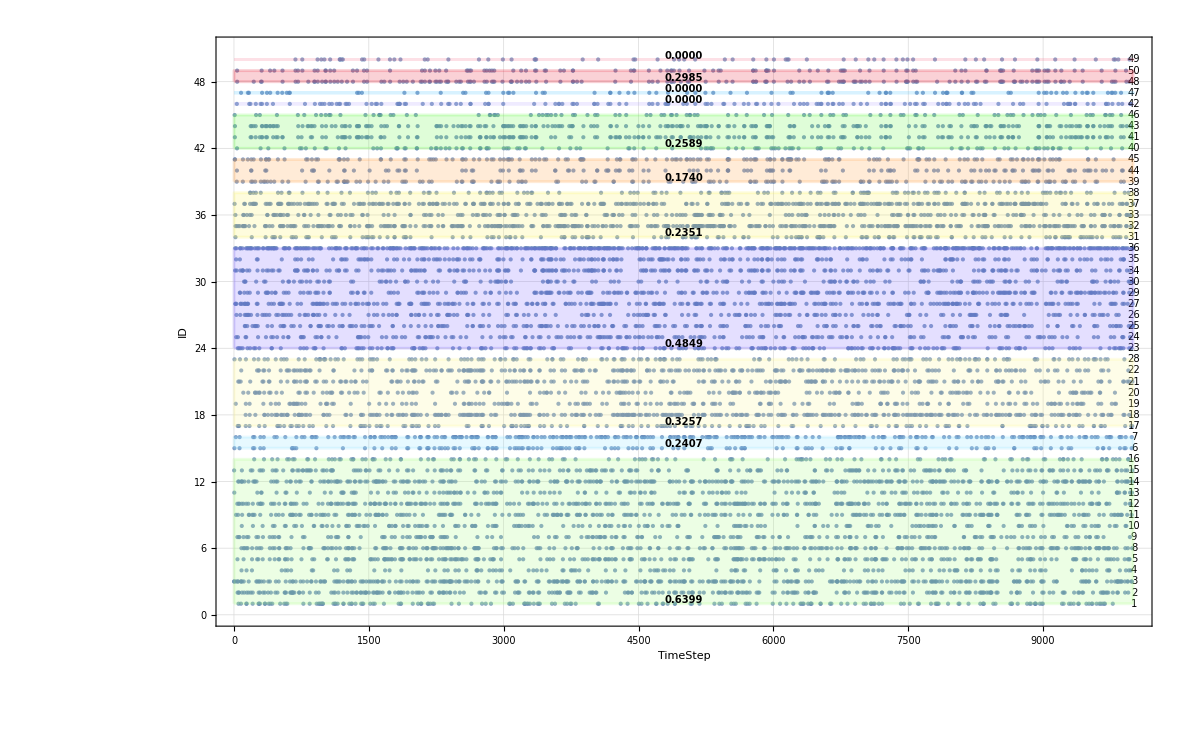
Transitions | Limiting
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(**)
data=RandomFunction[markov,{0,10000}];
tally=(data//Normal)[[All,All,2]][[1]]//Tally//Sort;
barChartFrequency=BarChart[tally[[All,2]],
ChartStyle->"LakeColors",
ChartLabels->tally[[All,1]],
ImageSize->650,
Frame->True,
FrameStyle->Thick,
FrameTicksStyle->Directive[8],
FrameLabel->(Style[#,25]&/@{"Node ID","Visit Frequency"})
];
songs=ListPlotSongWithCommunities[(data//Normal)[[1,All,2]],Map[ToExpression,clustersStrings,Infinity],colors,ImageSize->1200,TextSize->10];
{Range[Length[kernel]],MarkovProcessProperties[markov,"HoldingTimeMean"]}//MatrixForm;
limitMatrix=MarkovProcessProperties[markov,"LimitTransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
transitionsMatrix=MarkovProcessProperties[markov,"TransitionMatrix"]//MatrixPlot[#,PlotLegends->Placed[Automatic,Below],ColorFunction->"CherryTones",ImageSize->250]&;
matricesGrid=Grid[{Style[#,15]&/@{"Transitions","Limiting"},{transitionsMatrix,limitMatrix}}];
gridRandomWalker=Grid[{{Grid[{{matricesGrid},{barChartFrequency}}],songs}}]
```

Markov

```mathematica
MarkovProcessProperties[markov,"LimitTransitionMatrix"][[1]];
```

```mathematica
trans=Transpose[kernel];
{eVals,eVecs}=Eigensystem[trans]//N;
Normalize[eVecs[[1]],Total];
```

Normalize::nlnfa: The second argument Total is not a norm function that always returns a non-negative real number for any numeric argument.

{0.0180816,0.0268087,0.0319053,0.0128548,0.0225537,0.0140198,0.0261566,0.0273131,0.0182891,0.0142686,0.0248775,0.0308197,0.0157022,0.0321255,0.0199552,0.0131748,0.0146497,0.0308691,0.0158546,0.0147622,0.0208554,0.0213384,0.018782,0.0184242,0.0206853,0.0182832,0.0264676,0.0159737,0.0238206,0.0157219,0.0144611,0.0357833,0.0195889,0.0238365,0.0191359,0.0464523,0.0326747,0.0142337,0.01471,0.0116332,0.0234258,0.0143516,0.0234878,0.013913,0.0168157,0.00951675,0.0105348,0.0140621,0.00600032,0.0099887}

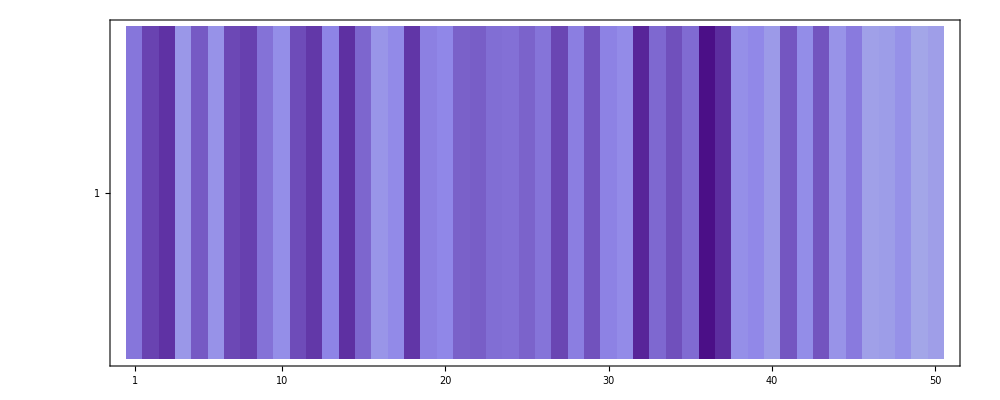

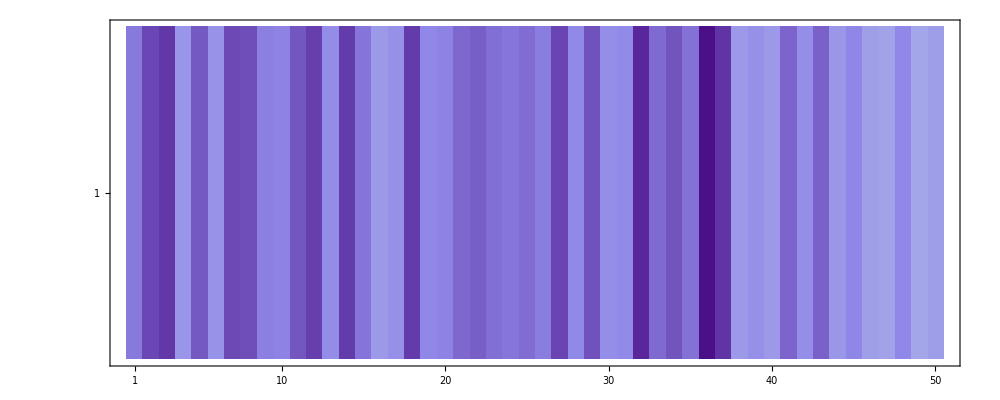

```mathematica
markov=DiscreteMarkovProcess[initialState,kernel];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length]
MatrixPlot[{markovPDF},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
MatrixPlot[{tally[[All,2]]},ColorFunction->ColorData[{"LakeColors","Reverse"}],ImageSize->1000]
```

```mathematica
{Range[markov[[1]]//Length],markovPDF}//Transpose
```

{{1,0.0180816},{2,0.0268087},{3,0.0319053},{4,0.0128548},{5,0.0225537},{6,0.0140198},{7,0.0261566},{8,0.0273131},{9,0.0182891},{10,0.0142686},{11,0.0248775},{12,0.0308197},{13,0.0157022},{14,0.0321255},{15,0.0199552},{16,0.0131748},{17,0.0146497},{18,0.0308691},{19,0.0158546},{20,0.0147622},{21,0.0208554},{22,0.0213384},{23,0.018782},{24,0.0184242},{25,0.0206853},{26,0.0182832},{27,0.0264676},{28,0.0159737},{29,0.0238206},{30,0.0157219},{31,0.0144611},{32,0.0357833},{33,0.0195889},{34,0.0238365},{35,0.0191359},{36,0.0464523},{37,0.0326747},{38,0.0142337},{39,0.01471},{40,0.0116332},{41,0.0234258},{42,0.0143516},{43,0.0234878},{44,0.013913},{45,0.0168157},{46,0.00951675},{47,0.0105348},{48,0.0140621},{49,0.00600032},{50,0.0099887}}

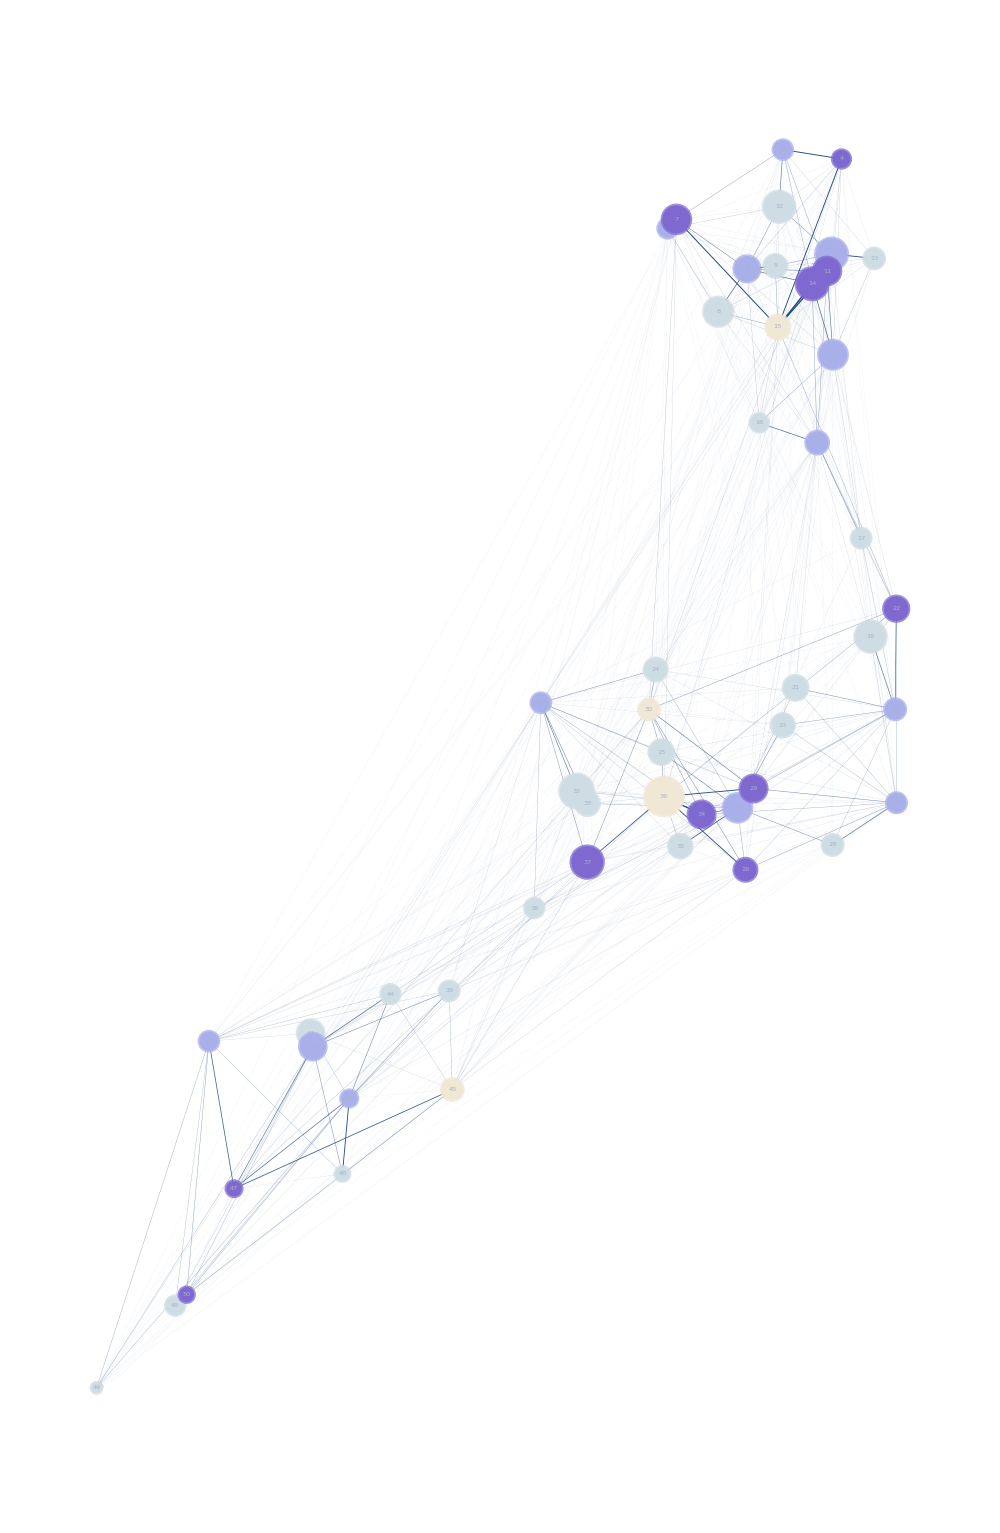

03_MarkovStationary.pdf

```mathematica
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.0025]]]]&/@Range[classesNumber];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
edgeshape2[e_,___]:={Arrowheads[{{.0075,.8}}],Arrow[e]}
graph = GraphTransitionsFrequenciesWithMax[
  {
Chop[normalizedMaskedMatrix,10^-1.5],
ToString /@ Range[Length[normalizedMaskedMatrix]]
   }, .25,
 VertexStyle->stylesListType,
VertexCoordinates->sampledCoordinates,
VertexSize -> Thread[VertexList[graph]->2*Log[1.5+3*Rescale[markovPDF]]],
VertexLabelStyle->6.5,
ImageSize->1000,
LineThickness->.0005,
EdgeShapeFunction->edgeshape2,
VariableStyle->"Both"
  ]
Export["03_MarkovStationary.pdf",%]
```

## Export Report

```mathematica
Grid[{{gridSinksAndSources},{gridRandomWalker}}]
Export["NetworkReport"<>StringPadLeft[ToString[(directionStrength*100)//Round],3,"0"]<>".pdf",%,ImageSize->5000,ImageResolution->500]
```